# Basis transformation of quantum states

Transform quantum state into a new basis

## Example Content

Quantum objects can be defined in a given basis, and then transformed into a new basis. Wolfram quantum framework fully support these transformation, as far as old and new basis match (same dimensionality).

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Define a 2D quantum state in computational basis:

```mathematica
ψ1=QuantumState[{1,ⅈ}]
```

QuantumState[…]

Transform it into Pauli-X basis and show the formula:

```mathematica
ψ2=QuantumState[ψ1,"X"];
ψ2["Formula"]
```

-((1-ⅈ) ψ_(x_-))/(√2)+((1+ⅈ) ψ_(x_+))/(√2)

```mathematica
ψ1["Formula"]
```

0+ⅈ 1

Test states are still the same:

```mathematica
ψ1==ψ2
```

True

Transform the state into Fourier basis and show the formula:

```mathematica
QuantumState[ψ1,"Fourier"]["Formula"]
```

-Graphics-

Define a random state in the Schwinger basis:

```mathematica
ψ1=QuantumState["RandomPure",QuantumBasis["Schwinger"]]
```

QuantumState[…]

Show the formula:

```mathematica
ψ1["Formula"]
```

(-0.161671+0.386228 ⅈ) S_00-(0.0475495+0.0612579 ⅈ) S_01-(0.0642457-0.295559 ⅈ) S_10+(0.374553+0.294794 ⅈ) S_11

Transform the state into new basis:

```mathematica
ψ2=QuantumState[ψ1,{2,2}]
```

QuantumState[…]

Show the formula of transformed basis:

```mathematica
ψ2["Formula"]
```

(-0.209221+0.32497 ⅈ) 00-(0.438799-0.000765014 ⅈ) 01+(0.310307+0.590354 ⅈ) 10-(0.114122-0.447486 ⅈ) 11

Test that states are still the same:

```mathematica
ψ1==ψ2
```

True

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

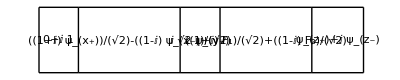

```mathematica
GraphicsRow[QuantumState[ψ1,#]["Formula"]&/@{2,"X","Y","Fourier","Z"},Frame->All]
```

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum basis

Quantum state

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.